# Compton Mess Around

## Parameters

```mathematica
Ee=150*10^6;
EL=1.17;
re=2.8179403262*10^-15;
me=0.511*10^6;
elecharge=1.602*10^-19;
γ[Ee_]:=Ee/me;
θmin=0;
θmax[Ee]:=ArcSin[1/γ[Ee]];
Xrec[Ee_,EL_]:=(4*γ[Ee]*EL)/me;
```

```mathematica
Q=32*10^-12;
Epulse=62*10^-6;
f=325*10^6;
σxy=3.2*10^-6;
σT=6.65*10^-29;
```

```mathematica
Ne[Q_]:=Q/elecharge;
NL[Epulse_,EL_]:=Epulse/(elecharge*EL);
```

## Equations dσ/dE_γ(from PRSTAB 12, 062801 (2009))

```mathematica
Eγ[Ee_,EL_,θ_]:=(4*γ[Ee]^2*EL)/(1+γ[Ee]^2*θ^2+Xrec[Ee,EL]);
endσdE[Ee_,EL_,Egam_]:=(π*re^2)/(2*γ[Ee]*EL)*(Ee^2/(4*γ[Ee]^4*EL^2)*(Egam/(Ee-Egam))^2-Ee/(γ[Ee]^2*EL)*Egam/(Ee-Egam)+Ee/(Ee-Egam)+(Ee-Egam)/Ee);
angdσdE[Ee_,EL_,θ_]:=(π*re^2)/(2*γ[Ee]*EL)*(Ee^2/(4*γ[Ee]^4*EL^2)*(Eγ[Ee,EL,θ]/(Ee-Eγ[Ee,EL,θ]))^2-Ee/(γ[Ee]^2*EL)*Eγ[Ee,EL,θ]/(Ee-Eγ[Ee,EL,θ])+Ee/(Ee-Eγ[Ee,EL,θ])+(Ee-Eγ[Ee,EL,θ])/Ee);
```

## Plotting dσ/dE_γ (Computed only to 1/γ opening angle)

```mathematica
Plot[endσdE[Ee,EL,Egam],{Egam,Eγ[Ee,EL,θmin],Eγ[Ee,EL,θmax[Ee]]},PlotRange->{{Eγ[Ee,EL,θmin],Eγ[Ee,EL,θmax[Ee]]},{0,8*10^-32}},AxesLabel->{"Scattered Photon Energy (eV)","Intensity, arb"}]
```

-Graphics-

```mathematica
Plot[angdσdE[Ee,EL,θ],{θ,θmin,θmax[Ee]},PlotRange->{{θmin,θmax[Ee]},{0,8*10^-32}},AxesLabel->{"Observation Angle (rad)","Intensity (arb)"}]
```

-Graphics-

## Equation dF/dσ and extension to dF/dE_γ

```mathematica
dFdσ[Q_,Epulse_,EL_,f_,σxy_]:=(Ne[Q]*NL[Epulse,EL]*f)/(2*π*σxy^2);
```

```mathematica
dFdE[Q_,Epulse_,EL_,f_,σxy_,Ee_,Egam_]:=dFdσ[Q,Epulse,EL,f,σxy]*endσdE[Ee,EL,Egam];
F[Q_,Epulse_,EL_,f_,σxy_]:=σT*(Ne[Q]*NL[Epulse,EL]*f)/(2*π*σxy^2);
angdFdE[Q_,Epulse_,EL_,f_,σxy_,Ee_,θ_]:=dFdσ[Q,Epulse,EL,f,σxy]*angdσdE[Ee,EL,θ];
```

## Plotting dF/dE_γ (Area = Flux) (Computed only to 1/γ opening angle)

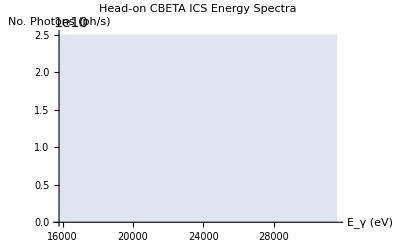

```mathematica
Plot[dFdE[Q,Epulse,EL,f,σxy,Ee,Egam],{Egam,Eγ[Ee,EL,θmin],Eγ[Ee,EL,θmax[Ee]]},PlotRange->{{Eγ[Ee,EL,θmin],Eγ[Ee,EL,θmax[Ee]]},{0,2.5*10^10}},AxesLabel->{"E_γ (eV)","No. Photons (ph/s)"},PlotLabel->"Head-on CBETA ICS Energy Spectra",Filling->Axis]
```

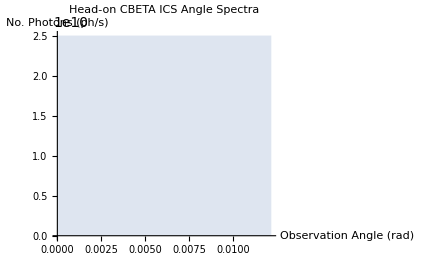

```mathematica
Plot[angdFdE[Q,Epulse,EL,f,σxy,Ee,θ],{θ,θmin,θmax[Ee]},PlotRange->{{θmin,θmax[Ee]},{0,2.5*10^10}},Filling->Axis,PlotLabel->"Head-on CBETA ICS Angle Spectra",AxesLabel->{"Observation Angle (rad)","No. Photons (ph/s)"}]
```

## CBETA Scattered Photon Energy

```mathematica
ϕ=(5*π)/180;
θob=0;
β[Ee_]:=Sqrt[1-1/γ[Ee]^2];
```

```mathematica
Eγang[EL_,Ee_,β_,θob_,ϕ_]:=(EL*(1-Cos[π-ϕ]))/(1-β*Cos[θob]+EL/Ee*(1-Cos[π-2*θob]))
```

```mathematica
Eγang[EL,Ee,β[Ee],θob,ϕ]
```

401414.

```mathematica
(*Kirstens method*)
Ekir[EL_,β_,ϕ_,θob_]:=EL*(1-β*Cos[π-ϕ])/(1-β*Cos[θob]);
```

```mathematica
Ekir[EL,β[Ee],ϕ,θob]
```

402492.